```mathematica
Subscript[H, J]=-n EJ(Cos[Subscript[φ, a]/n]+Cos[Subscript[φ, b]/n]+Cos[Subscript[φ, c]/n]+Cos[Subscript[φ, d]/n]);
Subscript[H, shunt]=EL/2(Subscript[φ, L1]^2+Subscript[φ, L2]^2+Subscript[φ, L3]^2+Subscript[φ, L4]^2);
({{Subscript[φ, a]}, {Subscript[φ, b]}, {Subscript[φ, c]}, {Subscript[φ, d]}})=({{1/2, 1/2, 1, 1/4}, {-1/2, 1/2, -1, 1/4}, {-1/2, -1/2, 1, 1/4}, {1/2, -1/2, -1, 1/4}}).({{Subscript[φ, x]}, {Subscript[φ, y]}, {Subscript[φ, z]}, {Subscript[φ, M]}});
solvecros=Flatten[Simplify[Solve[Subscript[φ, a]-Subscript[φ, L1]+Subscript[φ, L2]==Subscript[φ, ext]/4+2Pi Subscript[n, a]&&Subscript[φ, b]-Subscript[φ, L2]+Subscript[φ, L3]==Subscript[φ, ext]/4+2Pi Subscript[n, b]&&Subscript[φ, c]-Subscript[φ, L3]+Subscript[φ, L4]==Subscript[φ, ext]/4+2Pi Subscript[n, c]&&Subscript[φ, L1]+Subscript[φ, L2]+Subscript[φ, L3]+Subscript[φ, L4]==0,{Subscript[φ, L1],Subscript[φ, L2],Subscript[φ, L3],Subscript[φ, L4]}]/.Subscript[φ, M]->Subscript[φ, ext]+2Pi(Subscript[n, a]+Subscript[n, b]+Subscript[n, c]+Subscript[n, d])]/.{Subscript[n, a]->m,Subscript[n, b]->m,Subscript[n, c]->m,Subscript[n, d]->m}];
Subscript[H, shunt]=Simplify[Subscript[H, shunt]/.solvecros];
Subscript[H, J]=Simplify[Subscript[H, J]/.Subscript[φ, M]->Subscript[φ, ext]];
```

```mathematica
H=Subscript[H, J]+Subscript[H, shunt]
```

-4 EJ n (Cos[φ_ext/(4 n)] Cos[φ_x/(2 n)] Cos[φ_y/(2 n)] Cos[φ_z/n]+Sin[φ_ext/(4 n)] Sin[φ_x/(2 n)] Sin[φ_y/(2 n)] Sin[φ_z/n])+1/4 EL (φ_x^2+φ_y^2+2 φ_z^2)

```mathematica
Hx=Series[H,{Subscript[φ, x],0,4}]//Function[Y,Normal[Y+O[Subscript[φ, x]]^5]];
Hxy=Series[Hx,{Subscript[φ, y],0,4}]//Function[Y,Normal[Y+O[Subscript[φ, y]]^5]];
Hxyz=Series[Hxy,{Subscript[φ, z],0,4}]//Function[Y,Normal[Y+O[Subscript[φ, z]]^5]];
```

```mathematica
cool=CoefficientRules[Hxyz,{Subscript[φ, x],Subscript[φ, y],Subscript[φ, z]}];
power=Table[cool[[i,1,1]]+cool[[i,1,2]]+cool[[i,1,3]],{i,1,Length[cool]}];
hi=Flatten[Table[Flatten[Position[power,i]],{i,0,4}]];
hihi=Table[cool[[hi[[i]]]],{i,1,Length[hi]}];
For[i=1,i≤Length[hihi],i++,
hihi[[i,2]]=Collect[Simplify[hihi[[i,2]]],EJ]
]
hihi
```

{{0,0,0}→-4 EJ n Cos[φ_ext/(4 n)],{2,0,0}→EL/4+(EJ Cos[φ_ext/(4 n)])/(2 n),{0,2,0}→EL/4+(EJ Cos[φ_ext/(4 n)])/(2 n),{0,0,2}→EL/2+(2 EJ Cos[φ_ext/(4 n)])/n,{1,1,1}→-(EJ Sin[φ_ext/(4 n)])/n^2,{4,0,0}→-(EJ Cos[φ_ext/(4 n)])/(96 n^3),{2,2,0}→-(EJ Cos[φ_ext/(4 n)])/(16 n^3),{2,0,2}→-(EJ Cos[φ_ext/(4 n)])/(4 n^3),{0,4,0}→-(EJ Cos[φ_ext/(4 n)])/(96 n^3),{0,2,2}→-(EJ Cos[φ_ext/(4 n)])/(4 n^3),{0,0,4}→-(EJ Cos[φ_ext/(4 n)])/(6 n^3)}

```mathematica
H=Plus@@(hihi/.Rule[{a_,b_,c_},d_]:>Subscript[φ, XJ]^a Subscript[φ, YJ]^b Subscript[φ, ZJ]^c d);
```

```mathematica
EJ=2618.942;
EL=2.5EJ;
```

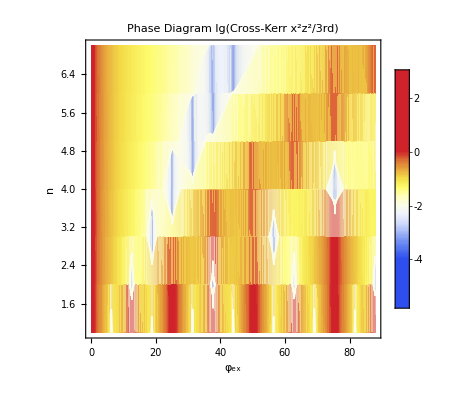

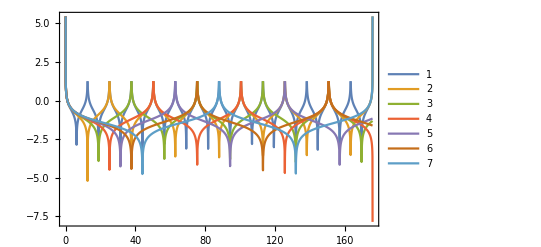

```mathematica
nmax=7;
tablen=Table[Log10[Abs[hihi[[8,2]]/hihi[[5,2]]]],{n,1,nmax}];

tablen1=Flatten[Table[{ i,n,tablen[[n]]/.Subscript[φ, ext]-> i},{i,0.1,4Pi nmax,0.1},{n,1,nmax}],1];

ListDensityPlot[
tablen1,
PlotLegends->Automatic,FrameLabel->{"φ_ex","n"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,Automatic},PlotLabel->Style["Phase Diagram lg(Cross-Kerr x^2z^2/3rd)",14],PlotRange->All,Mesh->3,MeshStyle->Black,MeshFunctions->{Boole[Greater[#3,-2]]&},ColorFunction->(ColorData[{"TemperatureMap",{-4,0}}]),ColorFunctionScaling->False
]
Plot[tablen,{Subscript[φ, ext],0,8π nmax},PlotRange->All,Frame->True,PlotLegends->Automatic]
```